Hidden Markov Model analysis of FRET photon traces

```mathematica
Needs["Fretica`"]
```

#### Introduction

Remark: The HMM analysis for FRET photon traces is currently only implemented for binned photon traces.
The probability P_i(S_A,S_D) that state i emits S_A acceptor photons and S_D donor photons in a bin is given by 
-Graphics-
F_A, F_D : fluorescence photons in acceptor and donor channels.
F = F_A+ F_D :total fluorescence photons (Poisson distributed)
B_A, B_D : background photons in acceptor and donor channels (Poisson distributed).
-Graphics-
ϵ : probability that a fluorescence photon is detected in the acceptor channel.
ρ_i(ϵ): distribution of ϵ for state i.
Ideally  ρ_i(ϵ)is a delta function for each state i. However, fast fluctuations of the transfer efficieny on the timescale of the binning might lead to a broadening. 
We describe this "intrinsic broadening" phenomenological by an empirical peak function. For this we use the PDF of the beta distribution:

```mathematica
ρ[ϵ_]=FBetaPeak[μ,ν][ϵ]
```

Piecewise[{{((1-ϵ)^(-1+ν-μ ν) ϵ^(-1+μ ν))/Beta[μ ν,ν-μ ν], 0<ϵ<1}, {0, True}}]

```mathematica
Manipulate[Plot[FBetaPeak[μ,10^logv][e],{e,0,1},PlotRange->All,PlotPoints->500, Frame->True],{{μ,0.5},0,1},{{logv,2},0.5,5}]
```

```mathematica
Integrate[FBetaPeak[μ,ν][ϵ],{ϵ,0,1},Assumptions->{0<μ<1,ν>0}]
```

1

```mathematica
Integrate[ϵ FBetaPeak[μ,ν][ϵ],{ϵ,0,1},Assumptions->{0<μ<1,ν>0}]
```

μ

```mathematica
Integrate[(ϵ-μ)^2 FBetaPeak[μ,ν][ϵ],{ϵ,0,1},Assumptions->{0<μ<1,ν>0}]
```

-((-1+μ) μ)/(1+ν)

#### Initialisation of the HMM system with binned photon traces or with photon-by-photon traces

```mathematica
?FFretHMMInitWithBinnedData
```

```mathematica
?FFretHMMInitWithPhotonByPhotonData
```

Missing[UnknownSymbol,FFretHMMInitWithPhotonByPhotonData]

```mathematica
?FFretHMMSetPhotonRates
```

```mathematica
?FFretHMMSetPinPfin
```

#### FFretHMMLogLikelihood, FHMMFretViterbi, and FFretHMMForwardBackward

```mathematica
?FFretHMMLogLikelihood
```

```mathematica
?FFretHMMViterbi
```

```mathematica
?FFretHMMForwardBackward
```

#### FFretHMMSimulateBinnedTrace

```mathematica
?FFretHMMSimulateBinnedTrace
```

## Demonstration for a two-state system

#### Definitions

```mathematica
Addt[dat_List]:={binning (Range[Length[dat]]-0.5),dat}ᵀ
SimulateAndPlot[ν_]:=(
{mcs,straj}=FFretHMMSimulateBinnedTrace[K,{{Frate, ϵ1, ν, bgA, bgD},{Frate, ϵ2, ν, bgA, bgD}},Smax, t, binning];
{na,nd}=mcsᵀ;
{ListPlot[{Addt@na,Addt@nd},Joined->True,PlotStyle->{Red,Darker@Green},ImageSize->500,AspectRatio->0.1,PlotRange->All,PlotLabel->"nu="<>ToString[ν]],
ListPlot[Addt@(na/(na+nd)),Joined->True,ImageSize->500,AspectRatio->0.1,PlotRange->All],
Histo[na/(na+nd+0.01),{0,1,0.02},PlotLabel->"nu="<>ToString[ν],ImageSize->200],Plot[{FBetaPeak[ϵ1,ν][e],FBetaPeak[ϵ2,ν][e]},{e,0,1},PlotRange->All,PlotPoints->500, Frame->True,PlotLabel->"nu="<>ToString[ν],ImageSize->200]}
)
```

#### Simulation of photon traces

```mathematica
Km[{k12_,k21_}]:=({{-k12, k21}, {k12, -k21}});
```

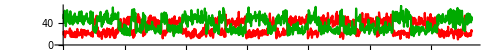
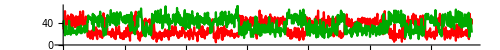
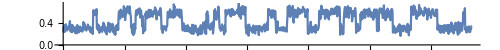
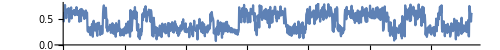
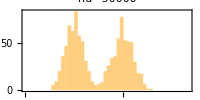
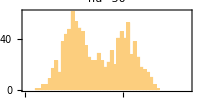
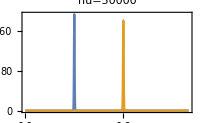
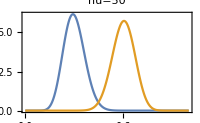

```mathematica
params={kf->40,ku->50};
K=Km[{kf,ku}/.params];
Frate=70000;
bgA=0;
bgD=0;
ϵ1=0.3;
ϵ2=0.6;
binning=0.001;
Smax=Round[3*Frate*binning];
t=1;
{SimulateAndPlot[50000],SimulateAndPlot[50]}ᵀ
```

#### LogLikelihood maximization (nu=50000, almost pure shot-noise broadening )

```mathematica
nu=50000;
params={kf->40,ku->50};
K=Km[{kf,ku}/.params];
Frate=70000;
bgA=0;bgD=0;
ϵ1=0.3;ϵ2=0.6;
binning=0.001;Smax=Round[3*Frate*binning];
t=10;
SimulateAndPlot[nu][[3;;4]]
FFretHMMInitWithBinnedData[{mcs},binning]
```

-Graphics-

```mathematica
ptraj1={{{Frate, ϵ1, nu},{Frate, ϵ2, nu}}, bgA, bgD};
FFretHMMSetPhotonRates[{ptraj1 }];
FindMaximum[FFretHMMLogLikelihood[Km[Abs@{kf,ku}]],{{kf,30},{ku,70}},PrecisionGoal->4,AccuracyGoal->4]
```

{-65178.1,{kf→41.2681,ku→51.2084}}

#### LogLikelihood maximization (nu=50, shot-noise and intrinsic broadening)

```mathematica
nu=50;
SimulateAndPlot[nu][[3;;4]]
FFretHMMInitWithBinnedData[{mcs},binning]
```

-Graphics-

Maximize log-likelihood assuming nu=50 (as simulated):

```mathematica
nu=50
ptraj1={{{Frate, ϵ1, nu},{Frate, ϵ2, nu}}, bgA, bgD};
FFretHMMSetPhotonRates[{ptraj1 }];
FindMaximum[FFretHMMLogLikelihood[Km[Abs@{kf,ku}]],{{kf,30},{ku,70}},PrecisionGoal->4,AccuracyGoal->4,Method->"PrincipalAxis"]
```

50

{-69061.9,{kf→35.5521,ku→41.722}}

Maximize log-likelihood assuming nu=50000 (almost pure shot-noise broadening):

```mathematica
nu=50000;
ptraj1={{{Frate, ϵ1, nu},{Frate, ϵ2, nu}}, bgA, bgD};
FFretHMMSetPhotonRates[{ptraj1 }];
FindMaximum[FFretHMMLogLikelihood[Km[Abs@{kf,ku}]],{{kf,30},{ku,50}},PrecisionGoal->4,AccuracyGoal->4,Method->"PrincipalAxis"]
```

{-71430.3,{kf→57.8927,ku→67.1614}}

| Related Guides
▪Fretica